```mathematica
data=Import["\\\\wsl.localhost\\Ubuntu-22.04\\home\\ahmedco31\\llm-distillation-analysis\\data\\responses_openai.csv","Tabular"];
```

```mathematica
data
```

```mathematica
responses=Normal[data[All,"response"]];
wordCounts=Length[StringSplit[#]]&/@responses;
```

Extract categories and group the word counts by them

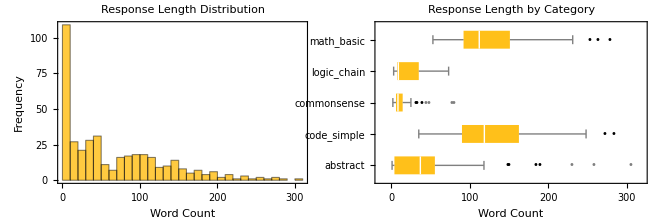

```mathematica
hist=Histogram[wordCounts,];
groupedData=GroupBy[Transpose[{Normal[data[All,"category"]],wordCounts}],First->Last];
box=BoxWhiskerChart[Values[groupedData],{"Outliers",{"MedianMarker",1,Directive[Thick,White]}},];
GraphicsRow[{hist,box},ImageSize->660,Spacings->20]
```

The heavily right-skewed distribution of response lengths is characteristic of a diverse query dataset aiming for broad domain coverage. Expected distillation behaviour. The boxplot shows how the word count is being distributed across the categories.

## Reasoning pattern detection

Distilling a model’s step-by-step reasoning process (Chain-of-Thought or CoT) is highly desirable because it allows an attacker to extract not just the final answer, but the underlying logic and problem-solving methodology of the target model. By tracking these markers, API providers can build anomaly detection systems to identify systematic queries designed to elicit these expensive reasoning chains, which strongly indicates a model extraction attack is occurring.

The bar chart below shows the average count of reasoning markers (like “first,” “then,” “therefore,” “step-by-step”) per response, grouped by category. High usage of reasoning markers in “math_basic”, “code_simple”, and “abstract” queries is shown.

Define markers and counting function

```mathematica
reasoningMarkers={RegularExpression["\\b(first|second|third|finally|therefore|thus|hence)\\b"],RegularExpression["\\b(step \\d+|step-by-step)\\b"],RegularExpression["\\b(because|since|given that)\\b"],RegularExpression["\\d+[\\.\\)]\\s"]};
countMarkers[text_String]:=Total[StringCount[text,reasoningMarkers,IgnoreCase->True]];
countMarkers[_]:=0;
```

Add the counts to the data

```mathematica
dataWithMarkers=InsertColumns[data,"reasoning_markers"->TabularColumn[countMarkers/@Normal[data[All,"response"]]]];
Tabular[dataWithMarkers,Background-><|"ColumnRules"->{"reasoning_markers"->RGBColor[0.24, 0.6, 0.8]}|>,ImageSize->Medium]
```

-Graphics-

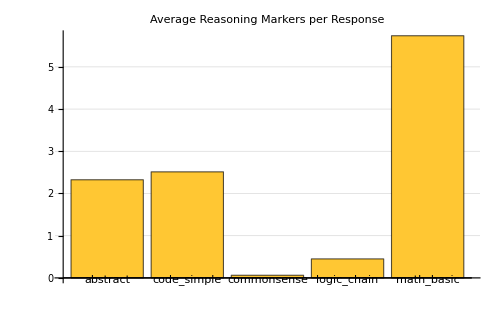

```mathematica
reasoningByCategory=Query[GroupBy["category"],<|"mean"->(Mean),"std"->(If[Length[#]>1,StandardDeviation[#],0.]&),"count"->Length|>,"reasoning_markers"][dataWithMarkers];
BarChart[Query[All,"mean"]@reasoningByCategory,]
```

```mathematica
Dataset@reasoningByCategory
```

## Query Pattern Analysis

I understand now why attackers add a randomly-lengthed intervals between queries, to mimic human behaviour when interacting with AI and avoid detection. When I made a fixed 20 seconds interval between queries, the histogram of inter-query intervals gives me away immediately. The variation in server response latency creates the skew we see in the histogram. The boxplot shows that the API’s response latency is fundamentally tied to the category of the query, rather than the length of the query interval.

Would seeing the server processing time regularly spikes to 5000ms raises a red flag even though inter-query timing looks random?

Extract timestamps, convert to seconds since 1900, sort, and calculate differences

```mathematica
intervals=Differences@Sort@N[AbsoluteTime/@Normal[data[All,"timestamp"]]];
```

```mathematica
medianInterval=Median@intervals;
```

Latencies and their mean

```mathematica
latencies=Normal[data[All,"latency_ms"]];
meanLatency=Mean[N@latencies];
```

Histogram vis.

```mathematica
lHist=Histogram[intervals,];
```

Latency by category: extract categories and group the latencies by category

```mathematica
latencyByCategory=GroupBy[Transpose[{Normal[data[All,"category"]],latencies}],First->Last];
```

```mathematica
lBox=BoxWhiskerChart[Values[latencyByCategory],];
```

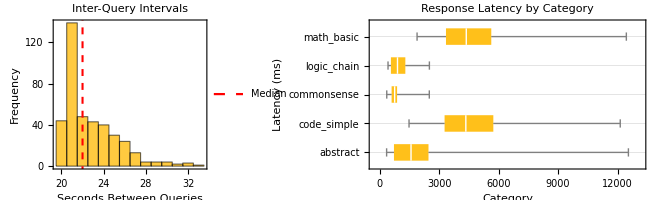

```mathematica
GraphicsRow[{lHist,lBox},ImageSize->660,Spacings->10]
```

## Prompt embeddings clustering

When you send prompts to a Large Language Model (LLM), it converts those text inputs into “embeddings”—massive lists of numbers (often thousands of dimensions long) that represent the mathematical “meaning” of the text.

As humans we cannot comprehend 1,000-dimensional space, we use UMAP (Uniform Manifold Approximation and Projection). UMAP is a dimensionality reduction algorithm that squashes those thousands of dimensions down to just two (the X and Y axes you see here). Crucially, UMAP preserves local structure: if two prompts mean similar things or trigger similar internal model behavior, they will fall in the same cluster.

Let’s start by extracting relevant values from the data

```mathematica
prompts=Normal[data[All,"prompt"]];
responses=Normal[data[All,"response"]];
categories=Normal[data[All,"category"]];
```

Then generate the embeddings. FeatureExtract handles state-of-the-art text embeddings natively, DimensionReduce supports UMAP. These embedding may not be exactly what different LLMs use, but they are close enough to study.

```mathematica
promptEmbeddings=FeatureExtract[prompts,"SentenceVector"];
responseEmbeddings=FeatureExtract[responses,"SentenceVector"];
```

```mathematica
Column[{Dimensions@promptEmbeddings,Dimensions@responseEmbeddings}]
```

{400,384}
{400,384}

UMAP Reduction

```mathematica
projections=DimensionReduce[promptEmbeddings,2,Method->"UMAP"];
```

Creating tooltips

```mathematica
plotPoints=Table[Tooltip[projections[[i]],Pane[Grid[{{Style["Prompt:",Bold],prompts[[i]]},{Style["Response:",Bold],responses[[i]]}},Alignment->{Left,Top}],{400,Automatic} ]],{i,Length[prompts]}];
```

Group the points by category

```mathematica
groupedData=GroupBy[Transpose[{categories,plotPoints}],First->Last];
```

The chart below proves that the LLM fundamentally treats these categories as entirely different computational tasks which forces the attackers to pick the categories they need knowledge for.

```mathematica
ListPlot[Values[groupedData],]
```

-Graphics-

Look at the tight, completely isolated clusters for math_basic (magenta nablas), code_simple (green deltas), and knowledge (cyan rhombuses). The model isn’t just generating text; it is routing these queries to highly specialized, distinct regions of its “brain” (its latent space).

Interestingly, the abstract prompts (orange circles) and logic_chain prompts (yellow squares) are broken into multiple tiny sub-clusters scattered around the edges. This tells us that “abstract” isn’t a single behavior to the LLM; it triggers several different internal semantic pathways.

When a company (like DeepSeek) attempts to distill a frontier model (like OpenAI’s), they don’t just want random data. They need to systematically map and extract the entire semantic landscape. If an attacker only queried the green cluster (commonsense), their cloned student model would be completely incapable of writing code or doing math.

## Infrastructure-level defense: timing-based anomaly detection

A latency vs tokens total chart with anomalies highlighted by Isolation Forest. Normally with prompt complexity getting higher, the latency gets higher, that is why we see the linear trend of the data. Having points outside the trend such as low token, high latency points in top left or high token, high latency in top right indicates unusual behaviour that worth checking. Attackers cannot easily fake the math of how GPUs generate tokens, making this a good defense tool against model extraction.

```mathematica
tokens=Normal[data[All,"tokens_total"]];
coords=Transpose[{tokens,latencies}];
```

Isolation Forest Anomaly Detection

```mathematica
detector=AnomalyDetection[features]
```

AnomalyDetectorFunction[…]

```mathematica
isAnomaly=detector[features,AcceptanceThreshold->0.05];
```

```mathematica
styledPoints=MapThread[Style[#1,If[#2,Red,Blue]]&,{coords,isAnomaly}];
```

```mathematica
plotData=GroupBy[Transpose[{categories,styledPoints}],First->Last];
```

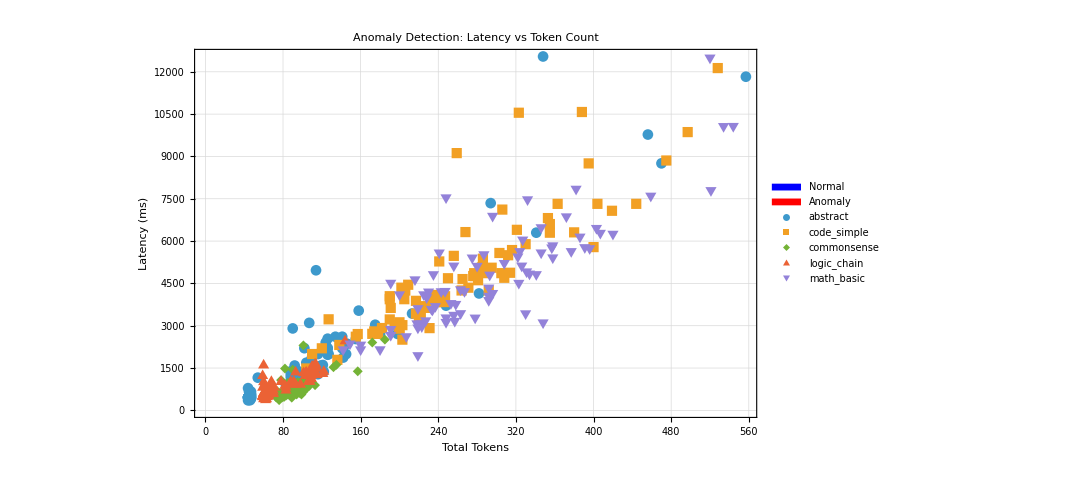

```mathematica
anomalyPlot=ListPlot[Values[plotData],PlotLegends->PointLegend[Automatic,Keys[plotData],LegendLabel->"Category"],PlotMarkers->Automatic,PlotStyle->PointSize[0.015],PlotLabel->Style["Anomaly Detection: Latency vs Token Count",16],AxesLabel->{"Total Tokens","Latency (ms)"},PlotTheme->"Detailed",ImageSize->{800,500},Epilog->Inset[SwatchLegend[{Blue,Red},{"Normal","Anomaly"}],Scaled[{0.15,0.85}]]]
```

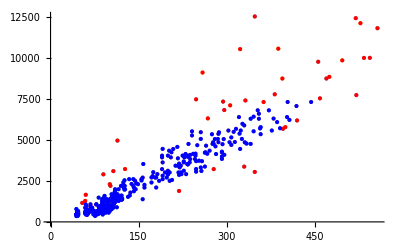

```mathematica
ListPlot[Values[plotData]]
```

## Infrastructure-level defense: timing-based anomaly detection

A latency vs tokens total chart with anomalies highlighted by Isolation Forest. Normally with prompt complexity getting higher, the latency gets higher, that is why we see the linear trend of the data. Having points outside the trend such as low token, high latency points in top left or high token, high latency in top right indicates unusual behaviour that worth checking. Attackers cannot easily fake the math of how GPUs generate tokens, making this a good defense tool against model extraction.

```mathematica
tokens=Normal[data[All,"tokens_total"]];
coords=Transpose[{tokens,latencies}];
dataPoints=Transpose[{categories,isAnomaly,coords}];
```

```mathematica
grouped=GroupBy[dataPoints,First->Rest,GroupBy[First->Last]];
```

```mathematica
categoryShapes=AssociationThread[DeleteDuplicates[categories]->{"●","■","◆","▲","▼"}];
anomalyColors=<|False->ColorData[97,1],True->ColorData[97,2]|>;
```

```mathematica
plots=Flatten@KeyValueMap[Function[{cat,anomalyGroup},KeyValueMap[Function[{isAnom,points},ListPlot[points,PlotStyle->anomalyColors[isAnom],PlotMarkers->{categoryShapes[cat],10},PlotLegends->None]],anomalyGroup]],grouped];
```

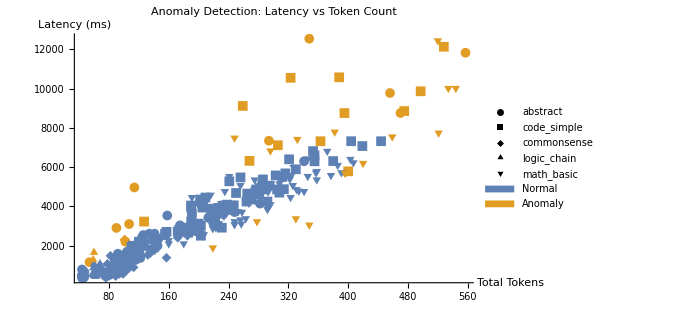

```mathematica
Legended[Show[plots,PlotRange->All,PlotLabel->Style["Anomaly Detection: Latency vs Token Count",16],AxesLabel->{"Total Tokens","Latency (ms)"},PlotTheme->"Detailed",ImageSize->{500,500}],(*The Custom dual-legend*)Placed[Grid[{{"Category","Anomaly Status"},{PointLegend[ConstantArray[Black,5],Keys[categoryShapes],LegendMarkers->categoryShapes/@Keys[categoryShapes]],SwatchLegend[{ColorData[97,1],ColorData[97,2]},{"Normal","Anomaly"}]}},Alignment->Top],Right]]
```

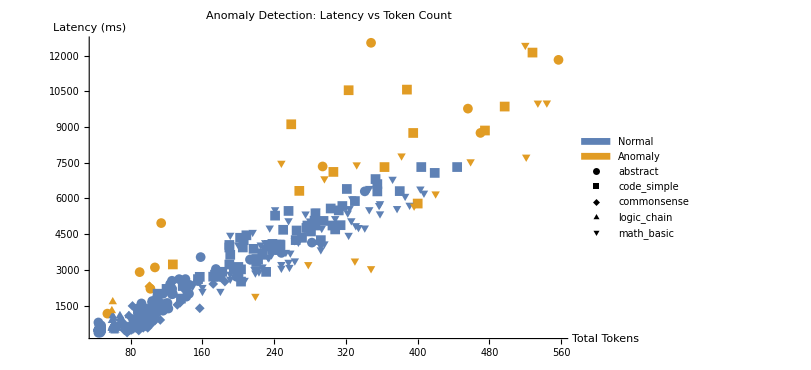

```mathematica
nativeBlue=ColorData[97,1];
nativeRed=ColorData[97,2];
anomalyColors=<|False->nativeBlue,True->nativeRed|>;

plots=Flatten@KeyValueMap[Function[{cat,anomalyGroup},KeyValueMap[Function[{isAnom,points},ListPlot[points,PlotStyle->anomalyColors[isAnom],PlotMarkers->{categoryShapes[cat],10},PlotLegends->None]],anomalyGroup]],grouped];

Legended[Show[plots,PlotRange->All,PlotLabel->Style["Anomaly Detection: Latency vs Token Count",16],AxesLabel->{"Total Tokens","Latency (ms)"},PlotTheme->"Detailed",ImageSize->600,BaseStyle->Bold],(*Pass a list to Legended to place multiple legends in different spots*){(*1. The Category legend stays on the Right*)Placed[PointLegend[ConstantArray[Black,5],Keys[categoryShapes],LegendMarkers->(categoryShapes/@Keys[categoryShapes]),LegendLabel->Style["Category",Bold]],Right],(*2. The Anomaly Status legend goes inside the plot,with a Frame*)Placed[SwatchLegend[{nativeBlue,nativeRed},{"Normal","Anomaly"},LegendLabel->Style["Anomaly Status",Bold],(*LegendFunction->Framed wraps the legend in a neat box*)LegendFunction->(Framed[#,Background->White,FrameStyle->Gray,RoundingRadius->5]&)],{0.85,0.25} (*Scaled coordinates inside the plot area*)]}]
```